```mathematica
Do[
Do[
Do[
vv=ToString[v];
ll=ToString[l];
nn=ToString[n];
gaux[v][l][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/LargeSimulation/GapD-l"<>ll<>"k-v"<>vv<>"-p0.1-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
velaux[v][l][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/LargeSimulation/VelD-l"<>ll<>"k-v"<>vv<>"-p0.1-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
avelaux[v][l][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/LargeSimulation/AveVel-l"<>ll<>"k-v"<>vv<>"-p0.1-"<>nn<>".txt",{Number,Number,Number,Number}];
,{n,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}}]
,{v,{9}}]
,{l,{5,10,20}}]
```

```mathematica
Do[
Do[
gap[v][l]=Sum[gaux[v][l][i]/16.,{i,1,16}];
vel[v][l]=Sum[velaux[v][l][i]/16.,{i,1,16}];
avel[v][l]=Sum[avelaux[v][l][i]/16.,{i,1,16}];
,{v,{9}}]
,{l,{5,10,20}}]
```

```mathematica
Do[
Do[
Do[
vv=ToString[v];
ll=ToString[l];
nn=ToString[n];
gaux[v][l][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/LargeSimulation/GapD-l"<>ll<>"k-v"<>vv<>"-p0.1-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
velaux[v][l][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/LargeSimulation/VelD-l"<>ll<>"k-v"<>vv<>"-p0.1-"<>nn<>".txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
avelaux[v][l][n]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/Result/LargeSimulation/AveVel-l"<>ll<>"k-v"<>vv<>"-p0.1-"<>nn<>".txt",{Number,Number,Number,Number}];
,{v,{9}}]
,{l,{40,80}}]
,{n,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}}]
Do[
Do[
gap[v][l]=Sum[gaux[v][l][i]/20.,{i,1,20}];
vel[v][l]=Sum[velaux[v][l][i]/20.,{i,1,20}];
avel[v][l]=Sum[avelaux[v][l][i]/20.,{i,1,20}];
,{v,{9}}]
,{l,{40,80}}]
```

```mathematica
gap[v][5]=Table[gap[v][5][[2*i]],{i,1,Length[gap[v][5]]/2}];
```

```mathematica
ngap="4";
nvel="4";
jj=StringToStream[ngap];
ng= Read[jj,Number];
ii=StringToStream[nvel];
nv= Read[ii,Number];
v=9;
Do[
Gap[v][l]=Table[{gap[v][l][[All,1]][[j]],Sum[gap[v][l][[All,i]][[j]],{i,2,ng+2}]},{j,1,Length[gap[v][l]]}];
Vel[v][l]=Table[{vel[v][l][[All,1]][[j]],Sum[vel[v][l][[All,i]][[j]],{i,2,nv+2}]},{j,1,Length[vel[v][l]]}];
AVel[v][l]=Table[{avel[v][l][[All,1]][[j]],avel[v][l][[All,2]][[j]]},{j,1,Length[avel[v][l]]}];
,{l,{5,10,20,40,80}}]
```

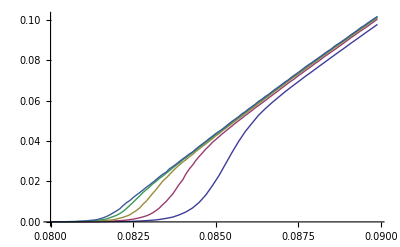

```mathematica
ListLinePlot[{Gap[v][5],Gap[v][10],Gap[v][20],Gap[v][40],Gap[v][80]}]
```

```mathematica
δ=0.00075;
Do[


g1[v][l]=Table[{Gap[v][l][[All,1]][[i]],Gap[v][l][[All,2]][[i]]},{i,1,Length[Gap[v][l]],2}];
g2[v][l]=Table[{Gap[v][l][[All,1]][[i]],Gap[v][l][[All,2]][[i]]},{i,2,Length[Gap[v][l]],2}];

ig[v][l]=Interpolation[Gap[v][l]];
ig1[v][l]=Interpolation[g1[v][l]];
ig2[v][l]=Interpolation[g2[v][l]];

(*dgdd[v][l]=Table[{x,(ig[v][l][x+δ]-ig[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0001}];
dg1dd[v][l]=Table[{x,(ig1[v][l][x+δ]-ig1[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0001}];
dg2dd[v][l]=Table[{x,(ig2[v][l][x+δ]-ig2[v][l][x-δ])/(2*δ)},{x,0.0815,0.087,0.0001}];*)

dgdd[v][l]=Table[{Gap[v][l][[All,1]][[i]],(Gap[v][l][[All,2]][[i+1]]-Gap[v][l][[All,2]][[i-1]])/(Gap[v][l][[All,1]][[i+1]]-Gap[v][l][[All,1]][[i-1]])},{i,2,Length[Gap[v][l]]-1}];

dg1dd[v][l]=Table[{g1[v][l][[All,1]][[i]],(g1[v][l][[All,2]][[i+1]]-g1[v][l][[All,2]][[i-1]])/(g1[v][l][[All,1]][[i+1]]-g1[v][l][[All,1]][[i-1]])},{i,2,Length[g1[v][l]]-1}];

dg2dd[v][l]=Table[{g2[v][l][[All,1]][[i]],(g2[v][l][[All,2]][[i+1]]-g2[v][l][[All,2]][[i-1]])/(g2[v][l][[All,1]][[i+1]]-g2[v][l][[All,1]][[i-1]])},{i,2,Length[g2[v][l]]-1}];

,{l,{5,10,20,40,80}}]
```

5

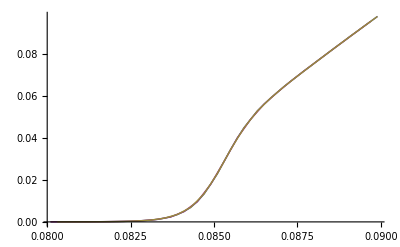

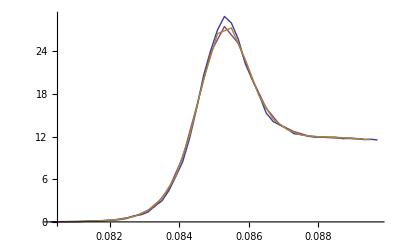

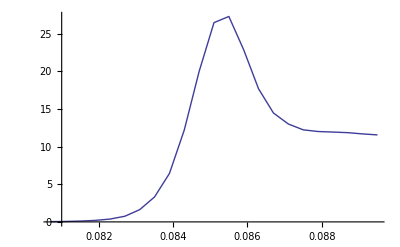

```mathematica
l=5
ListLinePlot[{Gap[v][l],g1[v][l],g2[v][l]}]
ListLinePlot[{dgdd[v][l],dg1dd[v][l],dg2dd[v][l]}]
ListLinePlot[{dg2dd[v][l]}]
```

```mathematica
maxdgdd[v]=Table[{l*1000,Max[dgdd[v][l][[All,2]]]},{l,{5,10,20,40,80}}]

Logmaxdgdd[v]=Table[{Log[maxdgdd[v][[All,1]][[i]]],Log[maxdgdd[v][[All,2]][[i]]]},{i,1,Length[maxdgdd[v]]}]

pmaxdgdd[v]=Table[{maxdgdd[v][[All,1]][[i]],Select[dgdd[v][maxdgdd[v][[All,1]][[i]]/1000],#[[2]]==maxdgdd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdgdd[v]]}]

vvpmaxdgdd[v]=Table[{pmaxdgdd[v][[All,1]][[i]],ig[v][pmaxdgdd[v][[All,1]][[i]]/1000][pmaxdgdd[v][[All,2]][[i]]]},{i,1,Length[pmaxdgdd[v]]}]


Logvvpmaxdgdd[v]=Table[{Log[vvpmaxdgdd[v][[All,1]][[i]]],Log[vvpmaxdgdd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdgdd[v]]}]



maxdg1dd[v]=Table[{l*1000,Max[dg1dd[v][l][[All,2]]]},{l,{5,10,20,40}}]

Logmaxdg1dd[v]=Table[{Log[maxdg1dd[v][[All,1]][[i]]],Log[maxdg1dd[v][[All,2]][[i]]]},{i,1,Length[maxdg1dd[v]]}]

pmaxdg1dd[v]=Table[{maxdg1dd[v][[All,1]][[i]],Select[dg1dd[v][maxdg1dd[v][[All,1]][[i]]/1000],#[[2]]==maxdg1dd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdg1dd[v]]}]

vvpmaxdg1dd[v]=Table[{pmaxdg1dd[v][[All,1]][[i]],ig1[v][pmaxdg1dd[v][[All,1]][[i]]/1000][pmaxdg1dd[v][[All,2]][[i]]]},{i,1,Length[pmaxdg1dd[v]]}]


Logvvpmaxdg1dd[v]=Table[{Log[vvpmaxdg1dd[v][[All,1]][[i]]],Log[vvpmaxdg1dd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdg1dd[v]]}]

maxdg2dd[v]=Table[{l*1000,Max[dg2dd[v][l][[All,2]]]},{l,{5,10,20,40,80}}]

Logmaxdg2dd[v]=Table[{Log[maxdg2dd[v][[All,1]][[i]]],Log[maxdg2dd[v][[All,2]][[i]]]},{i,1,Length[maxdg2dd[v]]}]

pmaxdg2dd[v]=Table[{maxdg2dd[v][[All,1]][[i]],Select[dg2dd[v][maxdg2dd[v][[All,1]][[i]]/1000],#[[2]]==maxdg2dd[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdg2dd[v]]}]

vvpmaxdg2dd[v]=Table[{pmaxdg2dd[v][[All,1]][[i]],ig2[v][pmaxdg2dd[v][[All,1]][[i]]/1000][pmaxdg2dd[v][[All,2]][[i]]]},{i,1,Length[pmaxdg2dd[v]]}]


Logvvpmaxdg2dd[v]=Table[{Log[vvpmaxdg2dd[v][[All,1]][[i]]],Log[vvpmaxdg2dd[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdg2dd[v]]}]
```

{{5000,28.9114},{10000,27.0868},{20000,20.6439},{40000,16.1994},{80000,14.7941}}

{{Log[5000],3.36424},{Log[10000],3.29905},{Log[20000],3.02742},{Log[40000],2.78497},{Log[80000],2.69423}}

{{5000,0.0853},{10000,0.0841},{20000,0.0833},{40000,0.0827},{80000,0.0822}}

{{5000,0.0286787},{10000,0.0237072},{20000,0.0181527},{40000,0.0128674},{80000,0.0081268}}

{{Log[5000],-3.5516},{Log[10000],-3.74198},{Log[20000],-4.00894},{Log[40000],-4.35306},{Log[80000],-4.81259}}

{{5000,27.5005},{10000,24.7514},{20000,19.7724},{40000,15.8555}}

{{Log[5000],3.3142},{Log[10000],3.20888},{Log[20000],2.98429},{Log[40000],2.76351}}

{{5000,0.0853},{10000,0.084},{20000,0.0832},{40000,0.0826}}

{{5000,0.0286787},{10000,0.0206957},{20000,0.0160537},{40000,0.0112812}}

{{Log[5000],-3.5516},{Log[10000],-3.87783},{Log[20000],-4.13182},{Log[40000],-4.48462}}

{{5000,27.3009},{10000,24.8356},{20000,19.7395},{40000,15.7133},{80000,13.6896}}

{{Log[5000],3.30692},{Log[10000],3.21228},{Log[20000],2.98262},{Log[40000],2.7545},{Log[80000],2.61664}}

{{5000,0.0855},{10000,0.0839},{20000,0.0831},{40000,0.0827},{80000,0.0823}}

{{5000,0.0344449},{10000,0.0186898},{20000,0.0141981},{40000,0.0128674},{80000,0.00949044}}

{{Log[5000],-3.3684},{Log[10000],-3.97978},{Log[20000],-4.25465},{Log[40000],-4.35306},{Log[80000],-4.65747}}

```mathematica
Logmaxdgdd[v]
Logvvpmaxdgdd[v]
pmaxdgdd[v]
```

{{Log[5000],3.36424},{Log[10000],3.29905},{Log[20000],3.02742},{Log[40000],2.78497},{Log[80000],2.69423}}

{{Log[5000],-3.5516},{Log[10000],-3.74198},{Log[20000],-4.00894},{Log[40000],-4.35306},{Log[80000],-4.81259}}

{{5000,0.0853},{10000,0.0841},{20000,0.0833},{40000,0.0827},{80000,0.0822}}

```mathematica
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=k0+c0*x^(-ex0)

nlfg1=NonlinearModelFit[Logvvpmaxdgdd[v],model1,{a0,b0},x];
nlfg1[{"BestFit","ParameterTable"}]

nlfg11=NonlinearModelFit[Logvvpmaxdg1dd[v],model1,{a0,b0},x];
nlfg11[{"BestFit","ParameterTable"}]

nlfg21=NonlinearModelFit[Logvvpmaxdg2dd[v],model1,{a0,b0},x];
nlfg21[{"BestFit","ParameterTable"}]

nlfg2=NonlinearModelFit[pmaxdgdd[v],model2,{c0,ex0},x];
nlfg2[{"BestFit","ParameterTable"}]

nlfg12=NonlinearModelFit[pmaxdg1dd[v],model2,{c0,ex0},x];
nlfg12[{"BestFit","ParameterTable"}]

nlfg22=NonlinearModelFit[pmaxdg2dd[v],model2,{c0,ex0},x];
nlfg22[{"BestFit","ParameterTable"}]
```

0.08122+c0 x^-ex0

{0.382787-0.452004 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.452004 | 0.0434637 | -10.3996 | 0.00189737
b0 | -0.382787 | 0.432545 | -0.884963 | 0.441353}

{0.197967-0.440459 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.440459 | 0.0184728 | -23.8437 | 0.00175432
b0 | -0.197967 | 0.177122 | -1.11769 | 0.379945}

{0.0942481-0.425801 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.425801 | 0.0720203 | -5.91224 | 0.00966501
b0 | -0.0942481 | 0.716738 | -0.131496 | 0.903706}

{0.08122+0.28131/x^0.496953, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.28131 | 0.0226405 | 12.4251 | 0.00112342
ex0 | 0.496953 | 0.00881237 | 56.3926 | 0.0000122832}

{0.08122+0.353494/x^0.52437, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.353494 | 0.0341159 | 10.3615 | 0.00918618
ex0 | 0.52437 | 0.0106903 | 49.0508 | 0.000415371}

{0.08122+0.396745/x^0.53501, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.396745 | 0.153663 | 2.58191 | 0.0816442
ex0 | 0.53501 | 0.0426109 | 12.5557 | 0.00108922}

```mathematica
a=nlfg1["ParameterTableEntries"][[1]][[1]]
a1=nlfg11["ParameterTableEntries"][[1]][[1]];
a2=nlfg21["ParameterTableEntries"][[1]][[1]];

c=nlfg2["ParameterTableEntries"][[1]][[1]]
c1=nlfg12["ParameterTableEntries"][[1]][[1]];
c2=nlfg22["ParameterTableEntries"][[1]][[1]];

ex=-nlfg2["ParameterTableEntries"][[2]][[1]]
ex1=-nlfg12["ParameterTableEntries"][[2]][[1]];
ex2=-nlfg22["ParameterTableEntries"][[2]][[1]];
```

-0.452004

0.28131

-0.496953

```mathematica
l1=80;
l2=10;
l3=20;
l4=40;
l5=5;
Do[

input[l]=Table[{(Gap[v][l][[All,1]][[i]]-(k0+c*(l*1000)^(ex))),Gap[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[Gap[v][l]]}];
input1[l]=Table[{(g1[v][l][[All,1]][[i]]-(k0+c1*(l*1000)^(ex1))),g1[v][l][[All,2]][[i]]*(l*1000)^(-a1)},{i,1,Length[g1[v][l]]}];
input2[l]=Table[{(g2[v][l][[All,1]][[i]]-(k0+c2*(l*1000)^(ex2))),g2[v][l][[All,2]][[i]]*(l*1000)^(-a2)},{i,1,Length[g2[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input[l][[All,1]][[i]])*(l*1000)^z,input[l][[All,2]][[i]]},{i,1,Length[input[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[(Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]])-(Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]])],{x,min,max}]/((max-min)*((Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]])-(Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]])));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf=z;

]
]

aux
"= zf"zf
```

0.0246857

0.39 = zf

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input1[l][[All,1]][[i]])*(l*1000)^z,input1[l][[All,2]][[i]]},{i,1,Length[input1[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

(*val=NIntegrate[Abs[(Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]])-(Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]])],{x,min,max}]/((max-min)*((Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]])-(Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]])))*)

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf1=z;

]
]

aux
"= zf1"zf1
```

0.0268289

0.19 = zf1

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(input2[l][[All,1]][[i]])*(l*1000)^z,input2[l][[All,2]][[i]]},{i,1,Length[input2[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zf2=z;

]
]

aux
"= zf2"zf2
```

0.0249369

0.21 = zf2

```mathematica
l1=5;
l2=10;
l3=20;
l4=40;
l5=80;
Do[

input[l]=Table[{(Gap[v][l][[All,1]][[i]]-(k0+c*(l*1000)^(ex)))*(l*1000)^(zf),Gap[v][l][[All,2]][[i]]*(l*1000)^(-a)},{i,1,Length[Gap[v][l]]}];
input1[l]=Table[{(g1[v][l][[All,1]][[i]]-(k0+c1*(l*1000)^(ex1)))*(l*1000)^(zf1),g1[v][l][[All,2]][[i]]*(l*1000)^(-a1)},{i,1,Length[g1[v][l]]}];
input2[l]=Table[{(g2[v][l][[All,1]][[i]]-(k0+c2*(l*1000)^(ex2)))*(l*1000)^(zf2),g2[v][l][[All,2]][[i]]*(l*1000)^(-a2)},{i,1,Length[g2[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

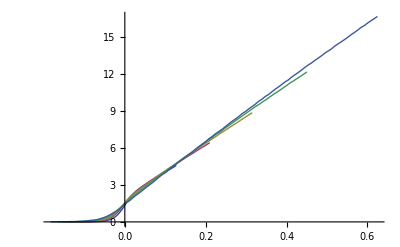

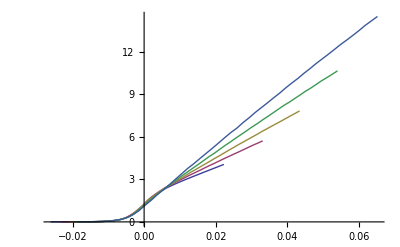

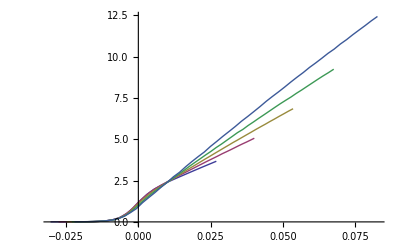

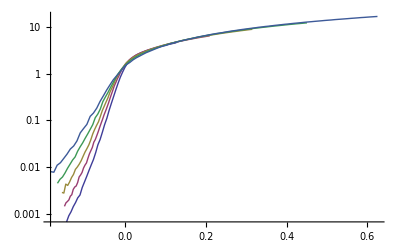

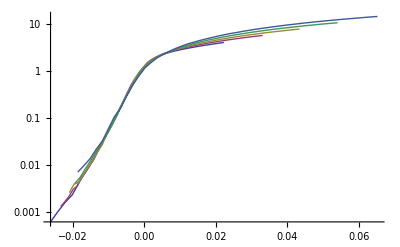

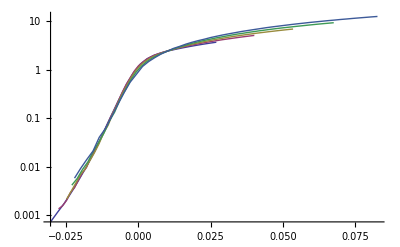

```mathematica
ListPlot[{input[5],input[10],input[20],input[40],input[80]},Joined->True]
ListPlot[{input1[5],input1[10],input1[20],input1[40],input1[80]},Joined->True]
ListPlot[{input2[5],input2[10],input2[20],input2[40],input2[80]},Joined->True]
ListLogPlot[{input[5],input[10],input[20],input[40],input[80]},Joined->True]
ListLogPlot[{input1[5],input1[10],input1[20],input1[40],input1[80]},Joined->True]
ListLogPlot[{input2[5],input2[10],input2[20],input2[40],input2[80]},Joined->True]
```

```mathematica
k0
c
ex
-a
zf
```

0.08122

0.28131

-0.496953

0.452004

0.39

```mathematica
k0
c1
ex1
-a1
zf1
```

0.08122

0.353494

-0.52437

0.440459

0.19

```mathematica
k0
c2
ex2
-a2
zf2
```

0.08122

0.396745

-0.53501

0.425801

0.21